## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
(* NumberTheory Package Test *)
Table[{n,n^2,n^3},{n,1,5}]//tf
Select[nCollatz[27],OddQ]
nFaulhaber[2,5]
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64
5 | 25 | 125

{27,41,31,47,71,107,161,121,91,137,103,155,233,175,263,395,593,445,167,251,377,283,425,319,479,719,1079,1619,2429,911,1367,2051,3077,577,433,325,61,23,35,53,5,1}

55

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\Algebra"];

<<Algebra`
```

```mathematica
G3=DirectProduct[Z[3],Z[3]]
Subgroups[SymmetricGroupAA[3]]//tf
```

Groupoid[{{0,0},{0,1},{0,2},{1,0},{1,1},{1,2},{2,0},{2,1},{2,2}},-Operation-]

Groupoid[{{1,2,3}},-Operation-]
Groupoid[{{1,2,3},{1,3,2}},-Operation-]
Groupoid[{{1,2,3},{2,1,3}},-Operation-]
Groupoid[{{1,2,3},{3,2,1}},-Operation-]
Groupoid[{{1,2,3},{2,3,1},{3,1,2}},-Operation-]
Groupoid[{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}},-Operation-]

```mathematica
CayleyTable[G3,Mode->Visual]
```

"Group properties""Element properties""Group Calculator"

* | {0,1} | {0,2} | {1,1} | {1,2} | {2,1} | {2,2}
{0,1} | {0,1} | {0,2} | {1,1} | {1,2} | {2,1} | {2,2}
{0,2} | {0,2} | {0,1} | {1,2} | {1,1} | {2,2} | {2,1}
{1,1} | {1,1} | {1,2} | {2,1} | {2,2} | {0,1} | {0,2}
{1,2} | {1,2} | {1,1} | {2,2} | {2,1} | {0,2} | {0,1}
{2,1} | {2,1} | {2,2} | {0,1} | {0,2} | {1,1} | {1,2}
{2,2} | {2,2} | {2,1} | {0,2} | {0,1} | {1,2} | {1,1}  Z[3] x U[3]

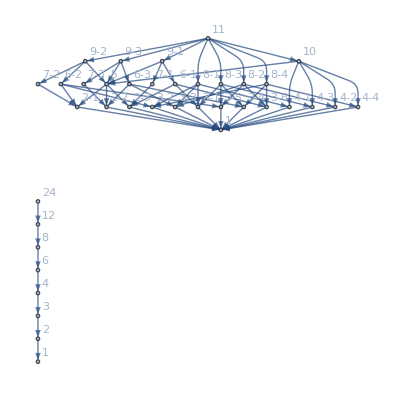

```mathematica
Import["C:\\Users\\Nilo\\lattice1.dot"]
```

```mathematica
G1=Alternating[4]
```

Groupoid[{{1,2,3,4},{1,3,4,2},{1,4,2,3},{2,1,4,3},{2,3,1,4},{2,4,3,1},{3,1,2,4},{3,2,4,1},{3,4,1,2},{4,1,3,2},{4,2,1,3},{4,3,2,1}},-Operation-]

```mathematica
Elements[G1]
```

{{1,2,3,4},{1,3,4,2},{1,4,2,3},{2,1,4,3},{2,3,1,4},{2,4,3,1},{3,1,2,4},{3,2,4,1},{3,4,1,2},{4,1,3,2},{4,2,1,3},{4,3,2,1}}

## Topic

### Definition / Theorem

This is text.

#### Example

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

# Algebra

Concepts

## Permutations

```mathematica
p1={2,3,1,4,5};
PermutationMatrix[p1]
p2={1,4,3,5,2};
PermutationMatrix[p2]
```

(1 | 2 | 3 | 4 | 5
2 | 3 | 1 | 4 | 5)

(1 | 2 | 3 | 4 | 5
1 | 4 | 3 | 5 | 2)

```mathematica
MultiplyPermutations[p1,p2,ProductOrder->LeftToRight]//PermutationMatrix
```

(1 | 2 | 3 | 4 | 5
4 | 3 | 1 | 5 | 2)

```mathematica
MultiplyPermutations[p1,p2]//PermutationMatrix
```

(1 | 2 | 3 | 4 | 5
2 | 4 | 1 | 5 | 3)

```mathematica
PermutationComposition[p1,p2]//PermutationMatrix
```

(1 | 2 | 3 | 4 | 5
2 | 4 | 1 | 5 | 3)

## Cycles

```mathematica
c1=Cycle[1,2,3];
c2=Cycle[2,4,5];
c3=ToCycles[MultiplyCycles[c1,c2,ProductOrder->LeftToRight]]
c3=ToCycles[MultiplyCycles[c1,c2,ProductOrder->LeftToRight],CycleAs->List]
FromCycles[{Cycle[1,4,5,2,3]}]
```

{Cycle[1,4,5,2,3]}

{{4,5,2,3,1}}

{4,3,1,5,2}

```mathematica
FromCycles[{Cycle[1,2,4,5,3]}]//PermutationMatrix
```

(1 | 2 | 3 | 4 | 5
2 | 4 | 1 | 5 | 3)

```mathematica
FromCycles[{{1,3},{2,4},{5},{6,7,8}}]//PermutationMatrix
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
3 | 4 | 1 | 2 | 5 | 7 | 8 | 6)

## Transpositions

```mathematica
Map[EvenQ[Length[#]]&,{ToTranspositions[{1,2,3}],ToTranspositions[{1,3,2}],ToTranspositions[{2,1,3}],ToTranspositions[{2,3,1}],ToTranspositions[{3,1,2}],ToTranspositions[{3,2,1}]}]
```

{True,False,False,True,True,False}

```mathematica
Map[EvenQ[Length[#]]&,Map[ToTranspositions[#]&,Permutations[Range[5]]]]//Counts
```

<|True→60,False→60|>

```mathematica
ToCycles[Permutations[Range[5]][[5]],CycleAs->List]
```

{{1},{2},{5,4,3}}

## Cycle Type

```mathematica
Map[Table[{k,Count[#,k]},{k,4}]&,Map[#&,IntegerPartitions[4]]]
```

{{{1,0},{2,0},{3,0},{4,1}},{{1,1},{2,0},{3,1},{4,0}},{{1,0},{2,2},{3,0},{4,0}},{{1,2},{2,1},{3,0},{4,0}},{{1,4},{2,0},{3,0},{4,0}}}

```mathematica
Map[Apply[Times,#]&,Map[Table[k^Count[#,k]Count[#,k]!,{k,4}]&,Map[#&,IntegerPartitions[4]]]]
```

{4,3,8,4,24}

Groups

## ToDo: Definitions

temp

## ToDo: Theorems

temp

Group Representations

## ToDo: Definitions

Defining Representation

Coset Representation

Regular Representation

Irreducible Representation

Submodule ( trivial or non-trivial )

(Ir)reducible G-Module

Orthogonal Complement

Maschke’s Theorem ( V as G-Module is sum of irreducible G-Modules )

Completely Reducible Representation

temp

temp

temp

temp

temp

temp

## ToDo: Theorems

temp

```mathematica
Binomial[n+1,2]+2Binomial[n+1,3]//Simplify
```

1/6 n (1+3 n+2 n^2)

```mathematica
f[n_]:=Sum[Binomial[n-1-j,j],{j,0,n-1}]
```

```mathematica
Table[{k,f[k]},{k,15}]//tf
```

1 | 1
2 | 1
3 | 2
4 | 3
5 | 5
6 | 8
7 | 13
8 | 21
9 | 34
10 | 55
11 | 89
12 | 144
13 | 233
14 | 377
15 | 610

```mathematica
Integrate[Sin[x]^(√x),{x,1,8}]
```

∫_1^8 Sin[x]^(√x)ⅆx

```mathematica
(.001)^(.001)
```

0.993116

```mathematica
Limit[x^x,x->0]
```

1

```mathematica
0^0
```

Power::indet: Indeterminate expression 0^0 encountered.

Indeterminate

## tmp

```mathematica
RSolve[{a[z]-a[z-1]==z^2,a[1]==1},a,z]
```

{{a→Function[{z},1/6 (1+z) (z+2 z^2)]}}

```mathematica
Series[1/(1/6 (1+z) (z+2 z^2)),{z,0,10}]
Series[z^0/(1-z)^2,{z,0,10}]
Series[z^1/(1-z)^3,{z,0,10}]
CoefficientList[Series[z^1/((1-z-z^2)^1),{z,0,10}],z]//Rest
CoefficientList[Series[z/(1-z)^2,{z,0,10}],z]//Rest
CoefficientList[Series[z/(1-z)^2,{z,0,10}],z][[2;;11]]
```

6/z-18+42 z-90 z^2+186 z^3-378 z^4+762 z^5-1530 z^6+3066 z^7-6138 z^8+12282 z^9-24570 z^10+O[z]^11

1+2 z+3 z^2+4 z^3+5 z^4+6 z^5+7 z^6+8 z^7+9 z^8+10 z^9+11 z^10+O[z]^11

z+3 z^2+6 z^3+10 z^4+15 z^5+21 z^6+28 z^7+36 z^8+45 z^9+55 z^10+O[z]^11

{1,1,2,3,5,8,13,21,34,55}

{1,2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Series[(1+z)/(1-z)^4,{z,0,10}]
```

1+5 z+14 z^2+30 z^3+55 z^4+91 z^5+140 z^6+204 z^7+285 z^8+385 z^9+506 z^10+O[z]^11

```mathematica
ClearAll[a,n,k]
a[0,0]:=1
a[1,1]:=1
a[0,1]:=1
a[1,0]:=1
a[n_,k_]:=a[n,k]=a[n-1,k-1]+a[n-1,k]
Grid[Table[a[i,j],{i,1,5},{j,1,5}]]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of a[-1020-1,-1018-1]+a[-1020-1,-1018].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of a[-1020-1,-1017-1]+a[-1020-1,-1017].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

1 | Hold[a[1,2]=a[1-1,2-1]+a[1-1,2]] | Hold[a[1,3]=a[1-1,3-1]+a[1-1,3]] | Hold[a[1,4]=a[1-1,4-1]+a[1-1,4]] | Hold[a[1,5]=a[1-1,5-1]+a[1-1,5]]
2 | Hold[a[2,2]=a[2-1,2-1]+a[2-1,2]] | Hold[a[2,3]=a[2-1,3-1]+a[2-1,3]] | Hold[a[2,4]=a[2-1,4-1]+a[2-1,4]] | Hold[a[2,5]=a[2-1,5-1]+a[2-1,5]]
Hold[a[3,1]=a[3-1,1-1]+a[3-1,1]] | Hold[a[3,2]=a[3-1,2-1]+a[3-1,2]] | Hold[a[3,3]=a[3-1,3-1]+a[3-1,3]] | Hold[a[3,4]=a[3-1,4-1]+a[3-1,4]] | Hold[a[3,5]=a[3-1,5-1]+a[3-1,5]]
Hold[a[4,1]=a[4-1,1-1]+a[4-1,1]] | Hold[a[4,2]=a[4-1,2-1]+a[4-1,2]] | Hold[a[4,3]=a[4-1,3-1]+a[4-1,3]] | Hold[a[4,4]=a[4-1,4-1]+a[4-1,4]] | Hold[a[4,5]=a[4-1,5-1]+a[4-1,5]]
Hold[a[5,1]=a[5-1,1-1]+a[5-1,1]] | Hold[a[5,2]=a[5-1,2-1]+a[5-1,2]] | Hold[a[5,3]=a[5-1,3-1]+a[5-1,3]] | Hold[a[5,4]=a[5-1,4-1]+a[5-1,4]] | Hold[a[5,5]=a[5-1,5-1]+a[5-1,5]]

```mathematica
Sum[Binomial[6,k]^2,{k,0,6}]
Binomial[12,6]
```

924

924

```mathematica
f[n_]:=n(n+1)(2n+1)/6
f[5]-f[4]
f[4]
Table[{k,f[k]},{k,0,5}]//tf
```

25

30

0 | 0
1 | 1
2 | 5
3 | 14
4 | 30
5 | 55